## Problem 1

In the bouncing ball example above, find the height of the tenth rebound, and the distance traveled by the ball after it touches the ground the tenth time. Compare this distance with the total distance traveled.

```mathematica
height=(2/3)^#&
```

(2/3)^#1&

```mathematica
height[10]
```

1024/59049

```mathematica
N[height[10],20]
```

0.017341529915832613592

1024/59049

WolframAlphaQueryResults

```mathematica
distance=∑_(i=1)^n height[i]
```

2^(1+n) 3^-n (-1+(3/2)^n)

```mathematica
distance//Simplify
```

-2 (-1+(2/3)^n)

```mathematica
∑_(n=1)^∞ -2 (-1+(2/3)^n)
```

Sum::div: Sum does not converge.

∑_(n=1)^∞ -2 (-1+(2/3)^n)

```mathematica
2(1-height[n])==distance//Simplify
```

True

```mathematica
distance=2(1-height[#])&
```

2 (1-height[#1])&

```mathematica
distance[10]
```

116050/59049

```mathematica
distance[11]
```

350198/177147

```mathematica
distance[Range[10]]
```

{2/3,10/9,38/27,130/81,422/243,1330/729,4118/2187,12610/6561,38342/19683,116050/59049}

```mathematica
Differences[distance[Range[10]]]
```

{4/9,8/27,16/81,32/243,64/729,128/2187,256/6561,512/19683,1024/59049}

```mathematica
totaldistance=1+2distance[#]&
```

1+2 distance[#1]&

```mathematica
totaldistance[Range[10]]
```

{7/3,29/9,103/27,341/81,1087/243,3389/729,10423/2187,31781/6561,96367/19683,291149/59049}

```mathematica
∑_(i=1)^∞ height[i]
```

2

```mathematica
∑_(i=1)^∞ totaldistance[i]
```

Sum::div: Sum does not converge.

∑_(i=1)^∞ (1+4 (1-(2/3)^i))

```mathematica
height[10]//N
```

0.0173415

```mathematica
Quantity[1, "Meters"]height[10]//N
```

0.0173415 m

```mathematica
height=(2/3)^#&
```

(2/3)^#1 (1 m)&

```mathematica
height[10]
```

1024/59049 m

```mathematica
∑_(i=1)^10 height[i]
```

116050/59049 m

```mathematica
∑_(i=1)^10 height[i]//N
```

1.96532 m

```mathematica
totaldistance=Quantity[1, "Meters"]+2(∑_(i=1)^# height[i])&
```

1 m+2 ∑_(i=1)^#1 height[i]&

```mathematica
totaldistance[10]
```

291149/59049 m

```mathematica
totaldistance[10]//N
```

4.93063 m

```mathematica
totaldistance[Range[10]]
```

{7/3 m,29/9 m,103/27 m,341/81 m,1087/243 m,3389/729 m,10423/2187 m,31781/6561 m,96367/19683 m,291149/59049 m}

```mathematica
Differences[totaldistance[Range[10]]]
```

{8/9 m,16/27 m,32/81 m,64/243 m,128/729 m,256/2187 m,512/6561 m,1024/19683 m,2048/59049 m}

```mathematica
totaldistance[10]-totaldistance[9]
```

2048/59049 m

```mathematica
1/2(totaldistance[10]-totaldistance[9])
```

1024/59049 m

```mathematica
distance=2(Quantity[1, "Meters"]-height[#])&
```

2 (1 m-height[#1])&

```mathematica
distance[10]-distance[9]
```

1024/59049 m

```mathematica
distance[10]-distance[9]//N
```

0.0173415 m

```mathematica
?distance
```

```mathematica
totaldistance[10]-totaldistance[9]//N
```

0.0346831 m

```mathematica
totaldistance[∞]
```

5 m

```mathematica
totaldistance[11]-totaldistance[10]
```

4096/177147 m

```mathematica
totaldistance[11]-totaldistance[10]//N
```

0.023122 m

```mathematica
distanceballtravels=2height[#]&
```

2 height[#1]&

```mathematica
distanceballtravels[10]//N
```

0.0346831 m

```mathematica
?totaldistance
```

```mathematica
totaldistance[9]
```

96367/19683 m

```mathematica
totaldistance[9]//N
```

4.89595 m

```mathematica
totaldistance[10]//N
```

4.93063 m

```mathematica
∑_(i=1)^n (2/3)^i-∑_(i=1)^(n-1) (2/3)^i
```

-2+2^n 3^(1-n)+2^(1+n) 3^-n (-1+(3/2)^n)

```mathematica
Simplify[-2+2^n 3^(1-n)+2^(1+n) 3^-n (-1+(3/2)^n)]
```

(3/2)^-n

```mathematica
Simplify[-2+2^n 3^(1-n)+2^(1+n) 3^-n (-1+(3/2)^n)]/.{n->10}
```

1024/59049

```mathematica
Simplify[-2+2^n 3^(1-n)+2^(1+n) 3^-n (-1+(3/2)^n)]/.{n->10}//N
```

0.0173415

```mathematica
distancebetweensuccessivebounces=2height[#]&
```

2 height[#1]&

```mathematica
distancebetweensuccessivebounces[10]
```

2048/59049 m

```mathematica
height=(2/3)^# Quantity[, "Meters"]&
```

(2/3)^#1 (1 m)&

```mathematica
distance=2(Quantity[1, "Meters"]-height[#])&
```

2 (1 m-height[#1])&

```mathematica
totaldistance=Quantity[1, "Meters"]+distance[#]&
```

1 m+distance[#1]&

```mathematica
height[10]
```

1024/59049 m

```mathematica
distance[10]
```

116050/59049 m

```mathematica
distance[10]-distance[9]
```

1024/59049 m

## Use equation 1.8 to find the fractions that are equivalent to the following repeating decimals

```mathematica
Rationalize[0.555]
```

111/200

```mathematica
11/20
```

11/20

```mathematica
N[11/20]
```

0.55

0.555555555555555555555555

WolframAlphaQueryResults

## Problem 5

0.58333

WolframAlphaQueryResults

## 1.9

0.857142857142

WolframAlphaQueryResults

The answer is 6/7.

## 1.11

0.678571428571428571

WolframAlphaQueryResults

I think the answer is 19/28.

## 1.15

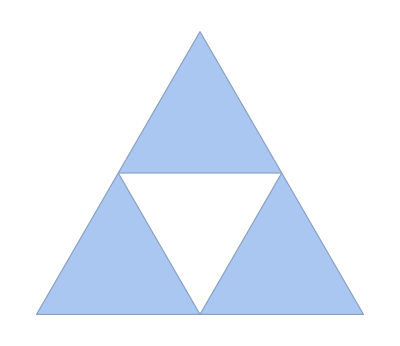
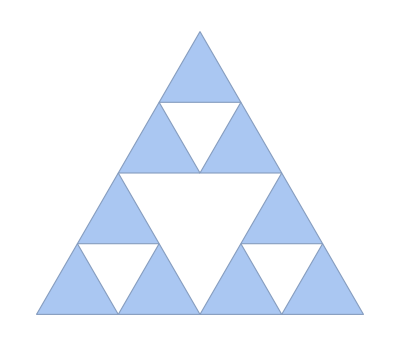
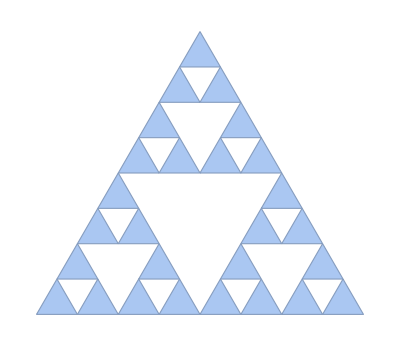
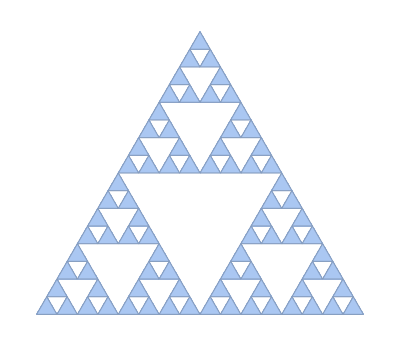
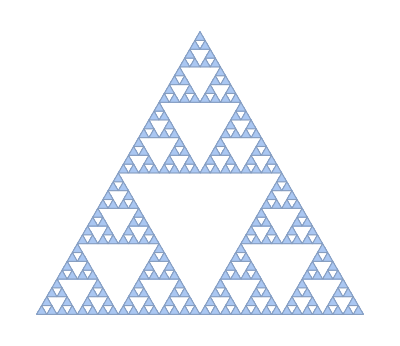
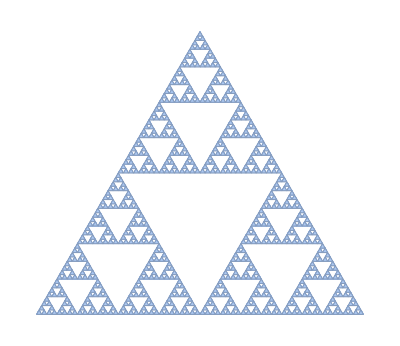

```mathematica
Table[SierpinskiMesh[i],{i,6}]
```

```mathematica
Table[SierpinskiMesh[i,3],{i,6}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
Table[Area[SierpinskiMesh[i]],{i,6}]
```

{0.32476,0.24357,0.182677,0.137008,0.102756,0.077067}

```mathematica
Table[RootApproximant@Area[SierpinskiMesh[i]],{i,10}]
```

{(3 √3)/16,(9 √3)/64,(27 √3)/256,Root0.137Root[1-7 #1-2 #1^2-#1^3-#1^4-8 #1^5-15 #1^6+9 #1^7-5 #1^8-9 #1^9+5 #1^10&,3]0.13700792520808494,Root0.103Root[1-10 #1+#1^2+14 #1^3+16 #1^4+4 #1^5-17 #1^6+14 #1^7-28 #1^8+#1^9&,2]0.10275594390606357,Root0.0771Root[-2+25 #1+12 #1^2+4 #1^3+5 #1^4+17 #1^5+6 #1^6-32 #1^7+21 #1^8&,2]0.07706695792954758,Root0.0578Root[-2+37 #1-44 #1^2+40 #1^3+59 #1^4+11 #1^5+7 #1^6&,2]0.05780021844716096,Root0.0434Root[-12+263 #1+307 #1^2+269 #1^3+19 #1^4&,2]0.04335016383537021,Root0.0325Root[-25+868 #1-3056 #1^2+275 #1^3&,1]0.03251262287652778,(2619-√1527481)/56720}

```mathematica
Table[RootApproximant@RegionMeasure[SierpinskiMesh[i,3]],{i,7}]
```

{1/(12 √2),1/(24 √2),1/(48 √2),1/(96 √2),(9809-√94888801)/18440,(9809-√94888801)/36880,(-4327+√19026417)/37936}